```mathematica
f[x]= HeavisideTheta[x]+Exp[-x]+Sinh[1]
```

ⅇ^-x+HeavisideTheta[x]+Sinh[1]

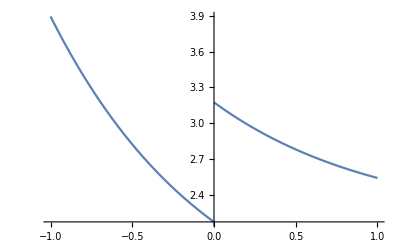

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
Integrate[f[x],{x,-1,1}]
```

1+4 Sinh[1]

```mathematica
N[1+4 Sinh[1]]
```

5.7008

-ⅇ^-x+HeavisideTheta[x]+Sinh[1]

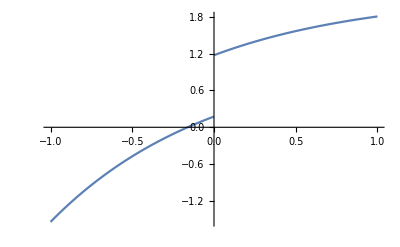

```mathematica
f1[x]= HeavisideTheta[x]-Exp[-x]+Sinh[1]
Plot[f1[x],{x,-1,1}]
```

```mathematica
f2[x]=(1-Sinh[1])HeavisideTheta[x]+0.5*Exp[x]
```

0.5 ⅇ^x+HeavisideTheta[x] (1-Sinh[1])

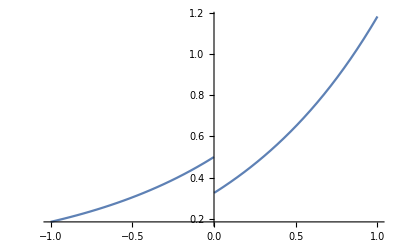

```mathematica
Plot[f2[x],{x,-1,1}]
```

```mathematica
Export["E:\\Computational_Physics\\hw4\\p2x.png",%8,"PNG"]
```

E:\Computational_Physics\hw4\p2x.png

```mathematica
Integrate[f2[x],{x,-1,1}]
```

1.

```mathematica
NumberForm[1.,16]
```

1.

```mathematica
NumberForm[1.,16]
```

1.

```mathematica
NumberForm[1.,{6,7}]
```

1.0000000

```mathematica
f2[-1]
```

f2[-1]

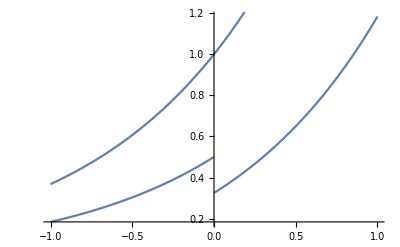

```mathematica
Show[Plot[f2[x],{x,-1,1}],Plot[Exp[x],{x,-1,1}]]
```

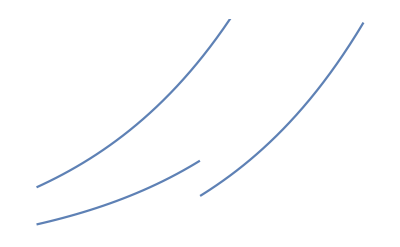

```mathematica
Show[%15,Axes->False]
```

```mathematica
Show[%16,Axes->True,AxesStyle->Black]
```

-Graphics-

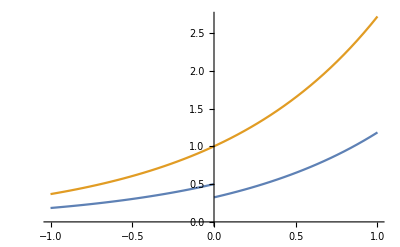

```mathematica
Plot[{(1-Sinh[1])HeavisideTheta[x]+0.5*Exp[x],Exp[x]},{x,-1,1}]
```

```mathematica
Plot[{(1-Sinh[1]) HeavisideTheta[x]+0.5 Exp[x],Exp[x]},{x,-1,1},Filling->Automatic]
```

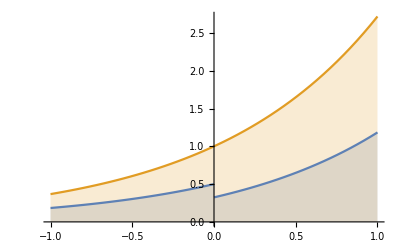

```mathematica
Plot[{(1-Sinh[1]) HeavisideTheta[x]+0.5 Exp[x],Exp[x]},{x,-1,1},Filling->Automatic]
```

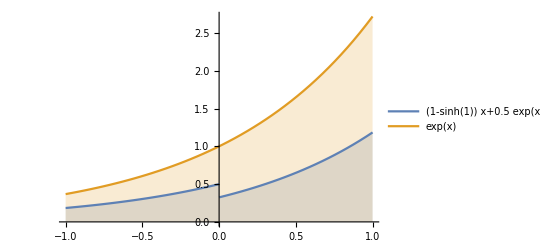

```mathematica
Plot[{(1-Sinh[1]) HeavisideTheta[x]+0.5 Exp[x],Exp[x]},{x,-1,1},Filling->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Plot[{(1-Sinh[1]) HeavisideTheta[x]+0.5 Exp[x],Exp[x]},{x,-1,1},Filling->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Plot[{f2[x],Exp[x]},{x,-1,1},Filling->f2]
```

-Graphics-

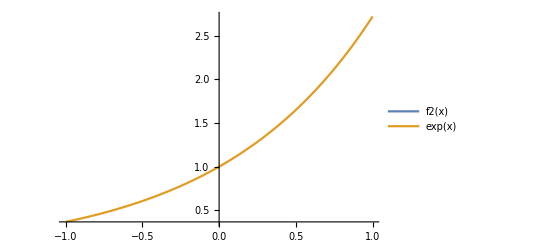

```mathematica
Plot[{f2[x],Exp[x]},{x,-1,1},Filling->{1->{2}},PlotLegends->"Expressions"]
```

```mathematica
1/(2ArcSin[1/Sqrt[3]])
```

1/(2 ArcSin[1/(√3)])

```mathematica
N[1/(2 ArcSin[1/(√3)])]
```

0.812374

```mathematica
N[2 ArcSin[1/(√3)]]
```

1.23096

```mathematica
1/(2Sinh[1])
```

Csch[1]/2

```mathematica
N[Csch[1]/2]
```

0.425459